{{x→InterpolatingFunction[{{0., 20.}}, <>],y→InterpolatingFunction[{{0., 20.}}, <>],z→InterpolatingFunction[{{0., 20.}}, <>]}}

Plot of Particle Position:

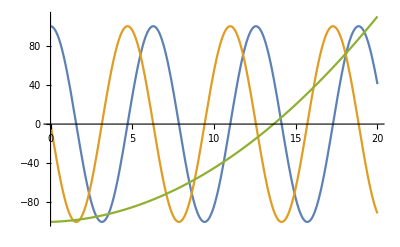

3D Plot of Particle Motion:

```mathematica
m=1;
q=1;
T=20;
size=100;
Ex=0;
Ey=0;
Ez=1;
Bx=0;
By=0;
Bz=1;
s=NDSolve[{m*x''[t]==q(Ex+y'[t]Bz-z'[t]By),m*y''[t]==q(Ey+z'[t]Bx-x'[t]Bz),m*z''[t]==q(Ez+x'[t]By-y'[t]Bx),x[0]==size,y[0]==0,z[0]==-size,x'[0]==0,y'[0]==-size,z'[0]==2size/T^2},{x,y,z},{t,0,T}]

"Plot of Particle Position:"
Plot[Evaluate[{x[t],y[t],z[t]}/.s],{t,0,T}]

"3D Plot of Particle Motion:"
plt=Plot3D[-2size,{x,-size,size},{y,-size,size},PlotRange->{-size,size}];
Animate[Show[plt,Graphics3D[{Blue,Sphere[{x[t],y[t],z[t]},3]}],BoxRatios->Automatic]/.s,{t,0,T},AnimationRate->T/4, AnimationRunning->False,RefreshRate->240]
```